## Data directories

```mathematica
(*DownloadDirectory="https://download.bhptoolkit.org/few/data/1PAT1R/";*)
```

```mathematica
DownloadDirectory=NotebookDirectory[];
```

```mathematica
Import[DownloadDirectory<>"Trajectory1PAT1R.h5"]
```

{/Energy/1PA/Grid,/Energy/1PA/dEdOmega,/Flux/AngularMomentum/0PA/Grid,/Flux/AngularMomentum/0PA/Horizon,/Flux/Energy/0PA/Infinity,/Flux/Energy/0PA/Grid,/Flux/Energy/0PA/Horizon,/Flux/Energy/1PA/Grid,/Flux/Energy/1PA/Infinity,/Flux/Energy/1PAchi1/Grid,/Flux/Energy/1PAchi1/Infinity,/Flux/Energy/1PAchi1/Horizon,/Flux/Energy/1PAchi2/Infinity,/Flux/Energy/1PAchi2/Grid,/Flux/Energy/1PAchi2/Horizon}

```mathematica
Import[DownloadDirectory<>"Amplitudes1PAT1R.h5"]
```

{/0PA/l3/m0/Infinity,/0PA/l3/m1/Infinity,/0PA/l3/m2/Infinity,/0PA/l3/m3/Infinity,/0PA/l2/m0/Infinity,/0PA/l2/m1/Infinity,/0PA/l2/m2/Infinity,/0PA/l4/m0/Infinity,/0PA/l4/m1/Infinity,/0PA/l4/m2/Infinity,/0PA/l4/m3/Infinity,/0PA/l4/m4/Infinity,/0PA/Grid,/0PA/l5/m0/Infinity,/0PA/l5/m1/Infinity,/0PA/l5/m2/Infinity,/0PA/l5/m3/Infinity,/0PA/l5/m4/Infinity,/0PA/l5/m5/Infinity,/1PA/l3/m0/Infinity,/1PA/l3/m1/Infinity,/1PA/l3/m2/Infinity,/1PA/l3/m3/Infinity,/1PA/l2/m0/Infinity,/1PA/l2/m1/Infinity,/1PA/l2/m2/Infinity,/1PA/l4/m0/Infinity,/1PA/l4/m1/Infinity,/1PA/l4/m2/Infinity,/1PA/l4/m3/Infinity,/1PA/l4/m4/Infinity,/1PA/Grid,/1PA/l5/m0/Infinity,/1PA/l5/m1/Infinity,/1PA/l5/m2/Infinity,/1PA/l5/m3/Infinity,/1PA/l5/m4/Infinity,/1PA/l5/m5/Infinity,/1PAchi1/l3/m0/Infinity,/1PAchi1/l3/m1/Infinity,/1PAchi1/l3/m2/Infinity,/1PAchi1/l3/m3/Infinity,/1PAchi1/Grid,/1PAchi1/l4/m0/Infinity,/1PAchi1/l4/m1/Infinity,/1PAchi1/l4/m2/Infinity,/1PAchi1/l4/m3/Infinity,/1PAchi1/l4/m4/Infinity,/1PAchi1/l2/m0/Infinity,/1PAchi1/l2/m1/Infinity,/1PAchi1/l2/m2/Infinity,/1PAchi1/l5/m0/Infinity,/1PAchi1/l5/m1/Infinity,/1PAchi1/l5/m2/Infinity,/1PAchi1/l5/m3/Infinity,/1PAchi1/l5/m4/Infinity,/1PAchi1/l5/m5/Infinity,/1PAchi2/l3/m0/Infinity,/1PAchi2/l3/m1/Infinity,/1PAchi2/l3/m2/Infinity,/1PAchi2/l3/m3/Infinity,/1PAchi2/l2/m0/Infinity,/1PAchi2/l2/m1/Infinity,/1PAchi2/l2/m2/Infinity,/1PAchi2/l4/m0/Infinity,/1PAchi2/l4/m1/Infinity,/1PAchi2/l4/m2/Infinity,/1PAchi2/l4/m3/Infinity,/1PAchi2/l4/m4/Infinity,/1PAchi2/Grid,/1PAchi2/l5/m0/Infinity,/1PAchi2/l5/m1/Infinity,/1PAchi2/l5/m2/Infinity,/1PAchi2/l5/m3/Infinity,/1PAchi2/l5/m4/Infinity,/1PAchi2/l5/m5/Infinity}

```mathematica
WaSABIdirectory=FileNameDrop[FindFile["WaSABI``"],-2];
WaSABIsfDataDirectory=FileNameJoin[{WaSABIdirectory,"InspiralModels"}];
WaSABIampDataDirectory=FileNameJoin[{WaSABIdirectory,"AmplitudeModels"}];
```

```mathematica
Flux0PAdirectory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/1SF_Flux/Schwarz_Circ"}];
Flux1PAchi1Directory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/1SF_Flux/Linear_Kerr_Circ"}];
Flux1PAdirectory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/2SF_Flux/Schwarz_Circ"}];
Flux1PAchi2Directory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/Leading_S2_Flux/Schwarz_Circ"}];
Energy1PAdirectory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/1SF_Local_Invariants/Schwarz_Circ"}];
Amp0PADirectory=FileNameJoin[{WaSABIampDataDirectory, "sf_amp_data/1SF/Schwarz_Circ"}];
Amp1PAchi1Directory=FileNameJoin[{WaSABIampDataDirectory, "sf_amp_data/1SF/Linear_Kerr_Circ"}];
Amp1PADirectory=FileNameJoin[{WaSABIampDataDirectory, "sf_amp_data/2SF/Schwarz_Circ"}];
Amp1PAchi2Directory=FileNameJoin[{WaSABIampDataDirectory, "sf_amp_data/Leading_S2/Schwarz_Circ"}];
```

## 1PA energy

### Data and interpolants

```mathematica
Energy1PAGrid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Energy/1PA/Grid"];
Energy1PAdEdOmegaData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Energy/1PA/dEdOmega"];
Energy1PAdEdOmegaOnGrid=Transpose[{Energy1PAGrid,Energy1PAdEdOmegaData}];
Energy1PAdEdOmega=Interpolation[Energy1PAdEdOmegaOnGrid,InterpolationOrder->8];
Energy1PAdEdOmegaCubicSpline=Interpolation[Energy1PAdEdOmegaOnGrid,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
Energy1PAdEdOmegaOnGridLoRes=Energy1PAdEdOmegaOnGrid[[;;;;8]];
Energy1PAdEdOmegaLoResCubicSpline=Interpolation[Energy1PAdEdOmegaOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
WaSABIRedshiftData=Import[Energy1PAdirectory<>"/1SFCircSchwarzRedshfit.m"];
```

```mathematica
WaSABIz = Interpolation[WaSABIRedshiftData, InterpolationOrder->8];
```

```mathematica
WaSABIEnergy1PA[x_]:=(1/2 WaSABIz[x]-x/3WaSABIz'[x]-1+Sqrt[1-3x]+x/6  (7-24x)/(1-3x)^(3/2))
```

```mathematica
dxdΩ[x_]:=2/(3 Sqrt[x])
```

```mathematica
WaSABI1PAdEdOmega[r0_]:=dxdΩ[1/r0]WaSABIEnergy1PA'[1/r0];
```

```mathematica
rmin1PAEnergy=Energy1PAGrid[[1]]
rmax1PAEnergy=Energy1PAGrid[[-1]]
```

6.

29.9883

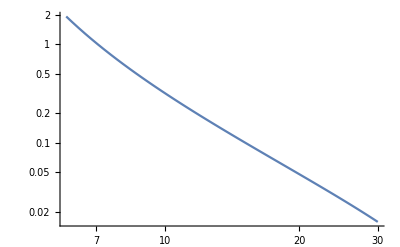

```mathematica
LogLogPlot[-Energy1PAdEdOmegaCubicSpline[r0],{r0,rmin1PAEnergy,rmax1PAEnergy}]
```

### Comparison of interpolating functions

```mathematica
FluxRelativeDifferenceOnGrid={#[[1]], Abs[1 - Energy1PAdEdOmegaCubicSpline[#[[1]]]/#[[2]]]} & /@ Energy1PAdEdOmegaOnGridLoRes;
```

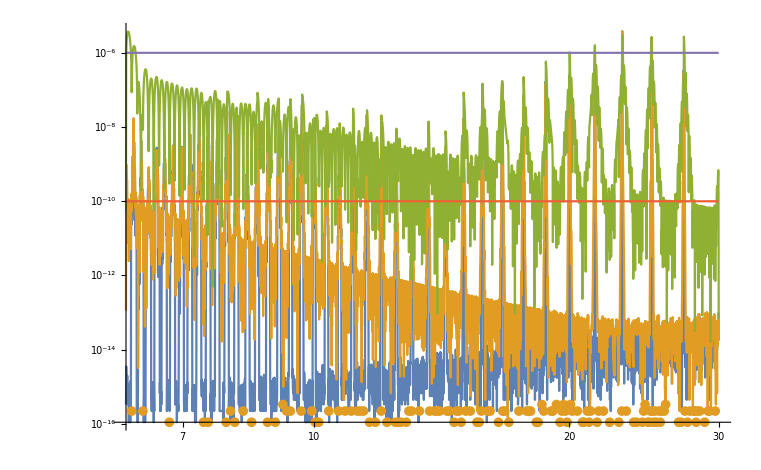

```mathematica
Show[LogLogPlot[{Abs[1-Energy1PAdEdOmega[r0]/WaSABI1PAdEdOmega[r0]],Abs[1-Energy1PAdEdOmegaCubicSpline[r0]/WaSABI1PAdEdOmega[r0]],Abs[1-Energy1PAdEdOmegaLoResCubicSpline[r0]/WaSABI1PAdEdOmega[r0]],10^-10,10^-6},{r0,rmin1PAEnergy,rmax1PAEnergy}],ListLogLogPlot[FluxRelativeDifferenceOnGrid,PlotStyle->{ColorData[97,2]}]]
```

## 0PA energy flux

### Data and interpolants

```mathematica
FluxEnergy0PAGrid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/0PA/Grid"];
FluxEnergy0PAInfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/0PA/Infinity"];
FluxEnergy0PAHorizonData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/0PA/Horizon"];
```

```mathematica
FluxEnergy0PAInfinityOnGrid=Transpose[{FluxEnergy0PAGrid,FluxEnergy0PAInfinityData}];
FluxEnergy0PAHorizonOnGrid=Transpose[{FluxEnergy0PAGrid,FluxEnergy0PAHorizonData}];
```

```mathematica
FluxEnergy0PAInfinity=Interpolation[FluxEnergy0PAInfinityOnGrid,InterpolationOrder->8];
FluxEnergy0PAInfinityCubicSpline=Interpolation[FluxEnergy0PAInfinityOnGrid,InterpolationOrder->3,Method->"Spline"];
FluxEnergy0PAHorizon=Interpolation[FluxEnergy0PAHorizonOnGrid,InterpolationOrder->8];
FluxEnergy0PAHorizonCubicSpline=Interpolation[FluxEnergy0PAHorizonOnGrid,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
FluxEnergy0PAInfinityOnGridLoRes=FluxEnergy0PAInfinityOnGrid[[;;;;8]];
FluxEnergy0PAInfinityLoResCubicSpline=Interpolation[FluxEnergy0PAInfinityOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
FluxEnergy0PAHorizonOnGridLoRes=FluxEnergy0PAHorizonOnGrid[[;;;;8]];
FluxEnergy0PAHorizonLoResCubicSpline=Interpolation[FluxEnergy0PAHorizonOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
WaSABIFluxEnergy0PAInfinityOnGrid=Import[Flux0PAdirectory<>"/1SFCircSchwarzDotEInf.m"];
```

```mathematica
WaSABIFluxEnergy0PAInfinity=Interpolation[WaSABIFluxEnergy0PAInfinityOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy0PAHorizonOnGrid=Import[Flux0PAdirectory<>"/1SFCircSchwarzDotEHorizon.m"];
```

```mathematica
WaSABIFluxEnergy0PAHorizon=Interpolation[WaSABIFluxEnergy0PAHorizonOnGrid,InterpolationOrder->8];
```

```mathematica
rmin0PAFlux=FluxEnergy0PAGrid[[1]]
rmax0PAFlux=FluxEnergy0PAGrid[[-1]]
```

6.

29.9883

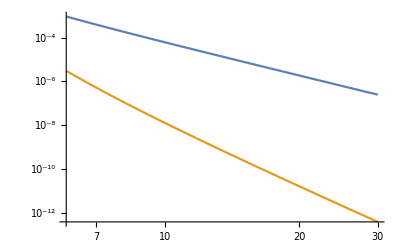

```mathematica
LogLogPlot[{FluxEnergy0PAInfinityCubicSpline[r0],FluxEnergy0PAHorizonCubicSpline[r0]},{r0,rmin0PAFlux,rmax0PAFlux}]
```

### Comparison of interpolating functions

InterpolatingFunction::dmval: Input value {4.2016} lies outside the range of data in the interpolating function. Extrapolation will be used.

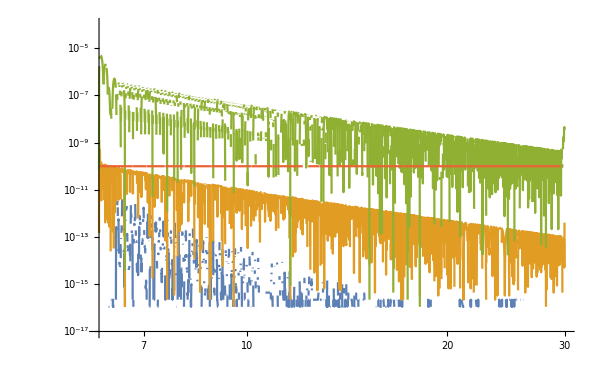

```mathematica
LogLogPlot[{Abs[1-FluxEnergy0PAInfinity[r0]/WaSABIFluxEnergy0PAInfinity[r0]],Abs[1-FluxEnergy0PAInfinityCubicSpline[r0]/WaSABIFluxEnergy0PAInfinity[r0]],Abs[1-FluxEnergy0PAInfinityLoResCubicSpline[r0]/WaSABIFluxEnergy0PAInfinity[r0]],10^-10},{r0,rmin0PAFlux,rmax0PAFlux},PlotRange->{{6,30},{10^-17,10^-4}}]
```

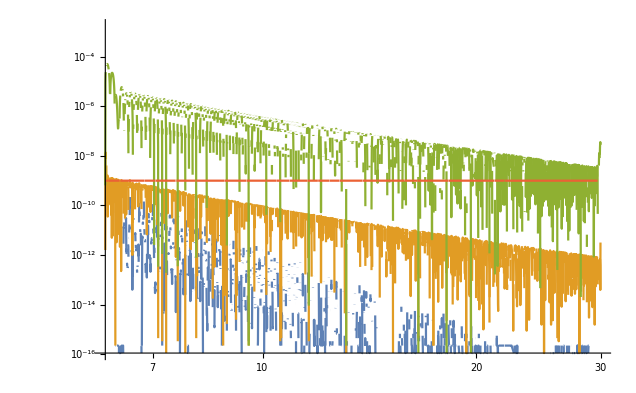

```mathematica
LogLogPlot[{Abs[1-FluxEnergy0PAHorizon[r0]/WaSABIFluxEnergy0PAHorizon[r0]],Abs[1-FluxEnergy0PAHorizonCubicSpline[r0]/WaSABIFluxEnergy0PAHorizon[r0]],Abs[1-FluxEnergy0PAHorizonLoResCubicSpline[r0]/WaSABIFluxEnergy0PAHorizon[r0]],10^-9},{r0,rmin0PAFlux,rmax0PAFlux}]
```

### Comparison of interpolant against raw WaSABI data

```mathematica
FluxEnergy0PAInfinityRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAInfinity[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAInfinityOnGrid);
FluxEnergy0PAInfinityCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAInfinityCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAInfinityOnGrid);
FluxEnergy0PAInfinityCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAInfinityCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAInfinityOnGrid);
FluxEnergy0PAInfinityLoResCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAInfinityLoResCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAInfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
FluxEnergy0PAHorizonRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAHorizon[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAHorizonOnGrid);
FluxEnergy0PAHorizonCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAHorizonCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAHorizonOnGrid);
FluxEnergy0PAHorizonLoResCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAHorizonLoResCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAHorizonOnGrid);
```

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

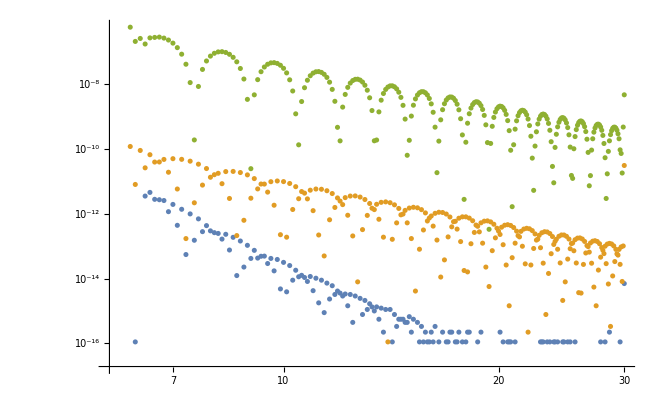

```mathematica
ListLogLogPlot[{FluxEnergy0PAInfinityRelativeDifferenceOnGrid,FluxEnergy0PAInfinityCubicSplineRelativeDifferenceOnGrid,FluxEnergy0PAInfinityLoResCubicSplineRelativeDifferenceOnGrid}]
```

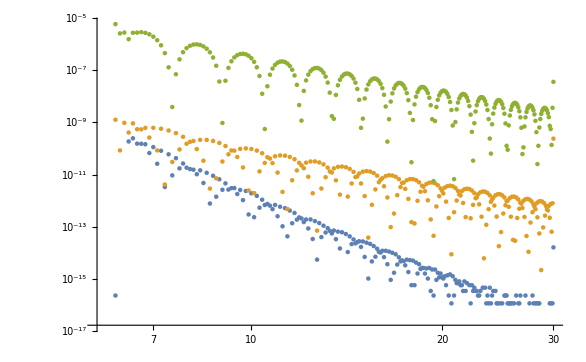

```mathematica
ListLogLogPlot[{FluxEnergy0PAHorizonRelativeDifferenceOnGrid,FluxEnergy0PAHorizonCubicSplineRelativeDifferenceOnGrid,FluxEnergy0PAHorizonLoResCubicSplineRelativeDifferenceOnGrid}]
```

## 0PA angular momentum flux

### Data and interpolants

```mathematica
FluxAngularMomentum0PAGrid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/AngularMomentum/0PA/Grid"];
FluxAngularMomentum0PAHorizonData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/AngularMomentum/0PA/Horizon"];
```

```mathematica
FluxAngularMomentum0PAHorizonOnGrid=Transpose[{FluxAngularMomentum0PAGrid,FluxAngularMomentum0PAHorizonData}];
```

```mathematica
FluxAngularMomentum0PAHorizon=Interpolation[FluxAngularMomentum0PAHorizonOnGrid,InterpolationOrder->8];
FluxAngularMomentum0PAHorizonCubicSpline=Interpolation[FluxAngularMomentum0PAHorizonOnGrid,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
FluxAngularMomentum0PAHorizonOnGridLoRes=FluxAngularMomentum0PAHorizonOnGrid[[;;;;8]];
FluxAngularMomentum0PAHorizonLoResCubicSpline=Interpolation[FluxAngularMomentum0PAHorizonOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
WaSABIFluxAngularMomentum0PAHorizon=Function[r0,r0^(3/2)WaSABIFluxEnergy0PAHorizon[r0]];
```

```mathematica
rminAngularMomentum0PAFlux=FluxAngularMomentum0PAGrid[[1]]
rmaxAngularMomentum0PAFlux=FluxAngularMomentum0PAGrid[[-1]]
```

6.

29.9883

```mathematica
FluxAngularMomentum0PAHorizonTest[r0_]:=FluxAngularMomentum0PAHorizon[r0]
```

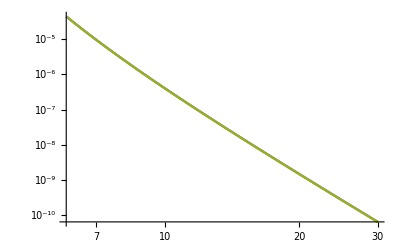

```mathematica
LogLogPlot[{FluxAngularMomentum0PAHorizon[r0],FluxAngularMomentum0PAHorizonCubicSpline[r0],WaSABIFluxAngularMomentum0PAHorizon[r0]},{r0,rminAngularMomentum0PAFlux,rmaxAngularMomentum0PAFlux}]
```

### Comparison of interpolating functions

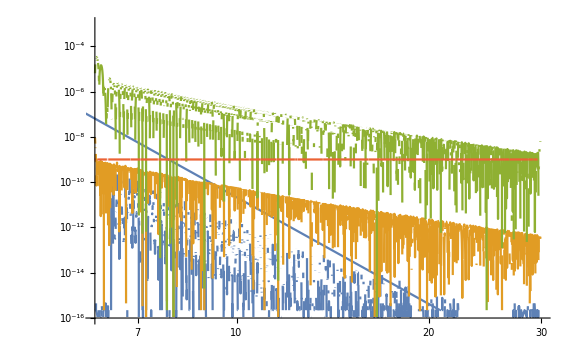

```mathematica
LogLogPlot[{Abs[1-FluxAngularMomentum0PAHorizon[r0]/WaSABIFluxAngularMomentum0PAHorizon[r0]],Abs[1-FluxAngularMomentum0PAHorizonCubicSpline[r0]/WaSABIFluxAngularMomentum0PAHorizon[r0]],Abs[1-FluxAngularMomentum0PAHorizonLoResCubicSpline[r0]/WaSABIFluxAngularMomentum0PAHorizon[r0]],10^-9},{r0,rminAngularMomentum0PAFlux,rmaxAngularMomentum0PAFlux},PlotRange->{{6,30},{10^-16,10^-3}}]
```

## 1PA energy flux

### Data and interpolants

```mathematica
FluxEnergy1PAGrid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PA/Grid"];
FluxEnergy1PAInfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PA/Infinity"];
```

```mathematica
FluxEnergy1PAInfinityOnGrid=Transpose[{FluxEnergy1PAGrid,FluxEnergy1PAInfinityData}];
```

```mathematica
FluxEnergy1PAInfinity=Interpolation[FluxEnergy1PAInfinityOnGrid,InterpolationOrder->8];
FluxEnergy1PAInfinityCubicSpline=Interpolation[FluxEnergy1PAInfinityOnGrid,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
FluxEnergy1PAInfinityOnGridLoRes=FluxEnergy1PAInfinityOnGrid[[;;;;8]];
FluxEnergy1PAInfinityLoResCubicSpline=Interpolation[FluxEnergy1PAInfinityOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
WaSABILogFluxEnergy1PAInfinityOnGrid=Import[Flux1PAdirectory<>"/2SFCircSchwarzDotEInf.m"];
```

```mathematica
WaSABILogFluxEnergy1PAInfinity=Interpolation[WaSABILogFluxEnergy1PAInfinityOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy1PAInfinityOnGrid=({Exp[#[[1]]],Re[Exp[#[[2]]]]}& /@ WaSABILogFluxEnergy1PAInfinityOnGrid);
```

```mathematica
WaSABIFluxEnergy1PAInfinity=Function[{r0},Re[Exp[WaSABILogFluxEnergy1PAInfinity[Log[r0]]]]];
```

```mathematica
rmin1PAFlux=FluxEnergy1PAGrid[[1]]
rmax1PAFlux=FluxEnergy1PAGrid[[-1]]
```

6.25

29.9884

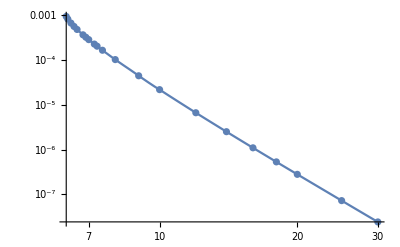

```mathematica
Show[LogLogPlot[-FluxEnergy1PAInfinityCubicSpline[r0],{r0,rmin1PAFlux,rmax1PAFlux}],ListLogLogPlot[Abs[WaSABIFluxEnergy1PAInfinityOnGrid]]]
```

### Comparison of interpolating functions

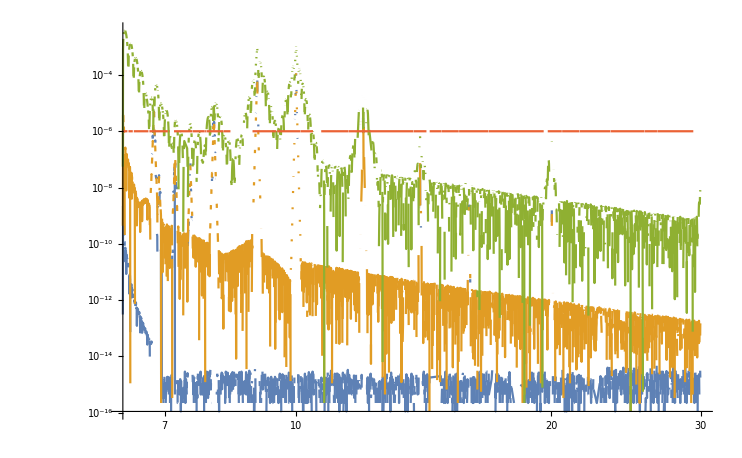

```mathematica
LogLogPlot[{Abs[1-FluxEnergy1PAInfinity[r0]/WaSABIFluxEnergy1PAInfinity[r0]],Abs[1-FluxEnergy1PAInfinityCubicSpline[r0]/WaSABIFluxEnergy1PAInfinity[r0]],Abs[1-FluxEnergy1PAInfinityLoResCubicSpline[r0]/WaSABIFluxEnergy1PAInfinity[r0]],10^-6},{r0,rmin1PAFlux,rmax1PAFlux}]
```

### Comparison of interpolant against raw WaSABI data

```mathematica
WaSABIFluxEnergy1PAInfinityOnGrid[[All,1]]
```

{6.25,6.3,6.4,6.5,6.6,6.8,6.9,7.,7.2,7.3,7.5,8.,9.,10.,12.,14.,16.,18.,20.,25.,30.,50.}

```mathematica
Intersection[FluxEnergy1PAGrid,WaSABIFluxEnergy1PAInfinityOnGrid[[All,1]],SameTest->(N[#1]==N[#2]&)]
```

{6.25}

```mathematica
FluxEnergy1PAInfinityRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAInfinity[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAInfinityOnGrid);
FluxEnergy1PAInfinityCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAInfinityCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAInfinityOnGrid);
FluxEnergy1PAInfinityLoResCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAInfinityLoResCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAInfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {50.} lies outside the range of data in the interpolating function. Extrapolation will be used.

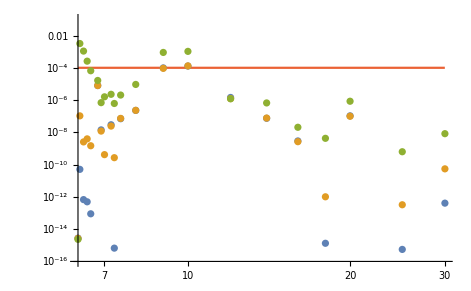

```mathematica
Show[LogLogPlot[10^-4,{r0,rmin1PAFlux,rmax1PAFlux},PlotStyle->{ColorData[97,3],ColorData[97,4]},PlotRange->{{rmin1PAFlux,rmax1PAFlux},{10^-16,.1}}],ListLogLogPlot[{FluxEnergy1PAInfinityRelativeDifferenceOnGrid,FluxEnergy1PAInfinityCubicRelativeDifferenceOnGrid,FluxEnergy1PAInfinityLoResCubicSplineRelativeDifferenceOnGrid}]]
```

## 1PA χ_1 energy flux

### Data and interpolants

```mathematica
FluxEnergy1PAchi1Grid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi1/Grid"];
FluxEnergy1PAchi1InfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi1/Infinity"];
FluxEnergy1PAchi1HorizonData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi1/Horizon"];
```

```mathematica
FluxEnergy1PAchi1InfinityOnGrid=Transpose[{FluxEnergy1PAchi1Grid,FluxEnergy1PAchi1InfinityData}];
FluxEnergy1PAchi1HorizonOnGrid=Transpose[{FluxEnergy1PAchi1Grid,FluxEnergy1PAchi1HorizonData}];
```

```mathematica
FluxEnergy1PAchi1Infinity=Interpolation[FluxEnergy1PAchi1InfinityOnGrid,InterpolationOrder->8];
FluxEnergy1PAchi1InfinityCubicSpline=Interpolation[FluxEnergy1PAchi1InfinityOnGrid,InterpolationOrder->3,Method->"Spline"];
FluxEnergy1PAchi1Horizon=Interpolation[FluxEnergy1PAchi1HorizonOnGrid,InterpolationOrder->8];
FluxEnergy1PAchi1HorizonCubicSpline=Interpolation[FluxEnergy1PAchi1HorizonOnGrid,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
FluxEnergy1PAchi1InfinityOnGridLoRes=FluxEnergy1PAchi1InfinityOnGrid[[;;;;8]];
FluxEnergy1PAchi1InfinityLoResCubicSpline=Interpolation[FluxEnergy1PAchi1InfinityOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
FluxEnergy1PAchi1HorizonOnGridLoRes=FluxEnergy1PAchi1HorizonOnGrid[[;;;;8]];
FluxEnergy1PAchi1HorizonLoResCubicSpline=Interpolation[FluxEnergy1PAchi1HorizonOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
WaSABIFluxEnergy1PAchi1InfinityOnGrid=Import[Flux1PAchi1Directory<>"/Slow_chi1_2SFCircSchwarzDotEInf.m"];
```

```mathematica
WaSABIFluxEnergy1PAchi1Infinity=Interpolation[WaSABIFluxEnergy1PAchi1InfinityOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy1PAchi1HorizonOnGrid=Import[Flux1PAchi1Directory<>"/Slow_chi1_2SFCircSchwarzDotEHorizon.m"];
```

```mathematica
WaSABIFluxEnergy1PAchi1Horizon=Interpolation[WaSABIFluxEnergy1PAchi1HorizonOnGrid,InterpolationOrder->8];
```

```mathematica
rmin1PAchi1Flux=FluxEnergy1PAchi1Grid[[1]]
rmax1PAchi1Flux=FluxEnergy1PAchi1Grid[[-1]]
```

6.1

29.9883

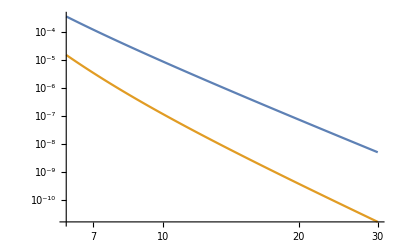

```mathematica
LogLogPlot[{-FluxEnergy1PAchi1InfinityCubicSpline[r0],-FluxEnergy1PAchi1HorizonCubicSpline[r0]},{r0,rmin1PAchi1Flux,rmax1PAchi1Flux}]
```

### Comparison of interpolating functions

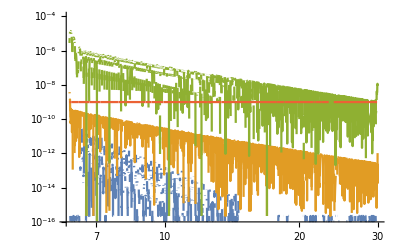

```mathematica
LogLogPlot[{Abs[1-FluxEnergy1PAchi1Infinity[r0]/WaSABIFluxEnergy1PAchi1Infinity[r0]],Abs[1-FluxEnergy1PAchi1InfinityCubicSpline[r0]/WaSABIFluxEnergy1PAchi1Infinity[r0]],Abs[1-FluxEnergy1PAchi1InfinityLoResCubicSpline[r0]/WaSABIFluxEnergy1PAchi1Infinity[r0]],10^-9},{r0,rmin1PAchi1Flux,rmax1PAchi1Flux},PlotRange->{{6,30},{10^-16,10^-4}}]
```

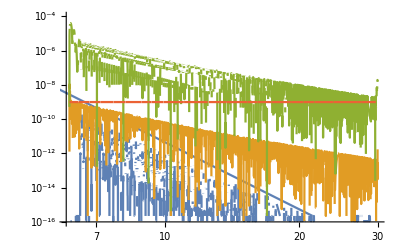

```mathematica
LogLogPlot[{Abs[1-FluxEnergy1PAchi1Horizon[r0]/WaSABIFluxEnergy1PAchi1Horizon[r0]],Abs[1-FluxEnergy1PAchi1HorizonCubicSpline[r0]/WaSABIFluxEnergy1PAchi1Horizon[r0]],Abs[1-FluxEnergy1PAchi1HorizonLoResCubicSpline[r0]/WaSABIFluxEnergy1PAchi1Horizon[r0]],10^-9},{r0,rmin1PAchi1Flux,rmax1PAchi1Flux},PlotRange->{{6,30},{10^-16,10^-4}}]
```

### Comparison of interpolant against raw WaSABI data

```mathematica
FluxEnergy1PAchi1InfinityRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi1Infinity[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi1InfinityOnGrid);
FluxEnergy1PAchi1InfinityCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi1InfinityCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi1InfinityOnGrid);
FluxEnergy1PAchi1InfinityLoResCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi1InfinityLoResCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi1InfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
FluxEnergy1PAchi1HorizonRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi1Horizon[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi1HorizonOnGrid);
FluxEnergy1PAchi1HorizonCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi1HorizonCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi1HorizonOnGrid);
FluxEnergy1PAchi1HorizonLoResCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi1HorizonLoResCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi1HorizonOnGrid);
```

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

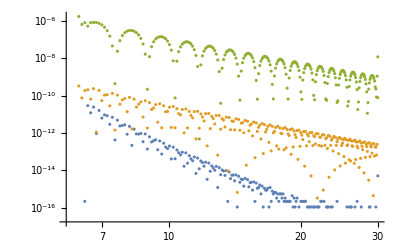

```mathematica
ListLogLogPlot[{FluxEnergy1PAchi1InfinityRelativeDifferenceOnGrid,FluxEnergy1PAchi1InfinityCubicSplineRelativeDifferenceOnGrid,FluxEnergy1PAchi1InfinityLoResCubicSplineRelativeDifferenceOnGrid}]
```

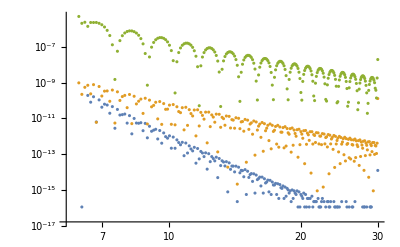

```mathematica
ListLogLogPlot[{FluxEnergy1PAchi1HorizonRelativeDifferenceOnGrid,FluxEnergy1PAchi1HorizonCubicSplineRelativeDifferenceOnGrid,FluxEnergy1PAchi1HorizonLoResCubicSplineRelativeDifferenceOnGrid}]
```

## 1PA χ_2 energy flux

### Data and interpolants

```mathematica
FluxEnergy1PAchi2Grid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi2/Grid"];
FluxEnergy1PAchi2InfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi2/Infinity"];
FluxEnergy1PAchi2HorizonData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi2/Horizon"];
```

```mathematica
FluxEnergy1PAchi2InfinityOnGrid=Transpose[{FluxEnergy1PAchi2Grid,FluxEnergy1PAchi2InfinityData}];
FluxEnergy1PAchi2HorizonOnGrid=Transpose[{FluxEnergy1PAchi2Grid,FluxEnergy1PAchi2HorizonData}];
```

```mathematica
FluxEnergy1PAchi2Infinity=Interpolation[FluxEnergy1PAchi2InfinityOnGrid,InterpolationOrder->8];
FluxEnergy1PAchi2InfinityCubicSpline=Interpolation[FluxEnergy1PAchi2InfinityOnGrid,InterpolationOrder->3,Method->"Spline"];
FluxEnergy1PAchi2Horizon=Interpolation[FluxEnergy1PAchi2HorizonOnGrid,InterpolationOrder->8];
FluxEnergy1PAchi2HorizonCubicSpline=Interpolation[FluxEnergy1PAchi2HorizonOnGrid,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
FluxEnergy1PAchi2InfinityOnGridLoRes=FluxEnergy1PAchi2InfinityOnGrid[[;;;;8]];
FluxEnergy1PAchi2InfinityLoResCubicSpline=Interpolation[FluxEnergy1PAchi2InfinityOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
FluxEnergy1PAchi2HorizonOnGridLoRes=FluxEnergy1PAchi2HorizonOnGrid[[;;;;8]];
FluxEnergy1PAchi2HorizonLoResCubicSpline=Interpolation[FluxEnergy1PAchi2HorizonOnGridLoRes,InterpolationOrder->3,Method->"Spline"];
```

```mathematica
WaSABIFluxEnergy1PAchi2InfinityOnGrid=Import[Flux1PAchi2Directory<>"/chi2_2SFCircSchwarzDotEInf.m"];
```

```mathematica
WaSABIFluxEnergy1PAchi2Infinity=Interpolation[WaSABIFluxEnergy1PAchi2InfinityOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy1PAchi2HorizonOnGrid=Import[Flux1PAchi2Directory<>"/chi2_2SFCircSchwarzDotEHorizon.m"];
```

```mathematica
WaSABIFluxEnergy1PAchi2Horizon=Interpolation[WaSABIFluxEnergy1PAchi2HorizonOnGrid,InterpolationOrder->8];
```

```mathematica
rmin1PAchi2Flux=FluxEnergy1PAchi2Grid[[1]]
rmax1PAchi2Flux=FluxEnergy1PAchi2Grid[[-1]]
```

6.1

29.9883

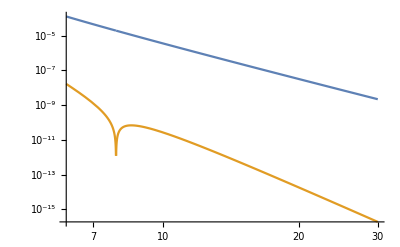

```mathematica
LogLogPlot[{-FluxEnergy1PAchi2InfinityCubicSpline[r0],Abs@FluxEnergy1PAchi2HorizonCubicSpline[r0]},{r0,rmin1PAchi2Flux,rmax1PAchi2Flux}]
```

### Comparison of interpolating functions

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

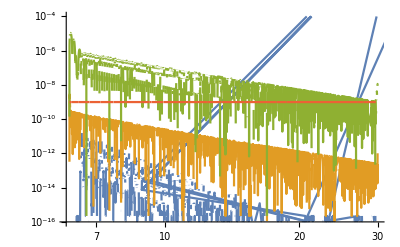

```mathematica
LogLogPlot[{Abs[1-FluxEnergy1PAchi2Infinity[r0]/WaSABIFluxEnergy1PAchi2Infinity[r0]],Abs[1-FluxEnergy1PAchi2InfinityCubicSpline[r0]/WaSABIFluxEnergy1PAchi2Infinity[r0]],Abs[1-FluxEnergy1PAchi2InfinityLoResCubicSpline[r0]/WaSABIFluxEnergy1PAchi2Infinity[r0]],10^-9},{r0,rmin1PAchi2Flux,rmax1PAchi2Flux},PlotRange->{{6,30},{10^-16,10^-4}}]
```

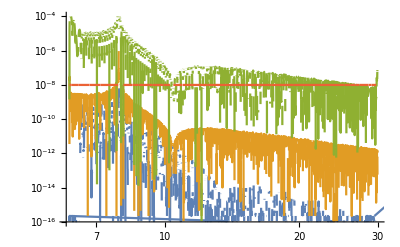

```mathematica
LogLogPlot[{Abs[1-FluxEnergy1PAchi2Horizon[r0]/WaSABIFluxEnergy1PAchi2Horizon[r0]],Abs[1-FluxEnergy1PAchi2HorizonCubicSpline[r0]/WaSABIFluxEnergy1PAchi2Horizon[r0]],Abs[1-FluxEnergy1PAchi2HorizonLoResCubicSpline[r0]/WaSABIFluxEnergy1PAchi2Horizon[r0]],10^-8},{r0,rmin1PAchi2Flux,rmax1PAchi2Flux},PlotRange->{{6,30},{10^-16,10^-4}}]
```

### Comparison of interpolant against raw WaSABI data

```mathematica
FluxEnergy1PAchi2InfinityRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi2Infinity[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi2InfinityOnGrid);
FluxEnergy1PAchi2InfinityCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi2InfinityCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi2InfinityOnGrid);
FluxEnergy1PAchi2InfinityLoResCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi2InfinityLoResCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi2InfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
FluxEnergy1PAchi2HorizonRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi2Horizon[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi2HorizonOnGrid);
FluxEnergy1PAchi2HorizonCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi2HorizonCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi2HorizonOnGrid);
FluxEnergy1PAchi2HorizonLoResCubicSplineRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi2HorizonLoResCubicSpline[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi2HorizonOnGrid);
```

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

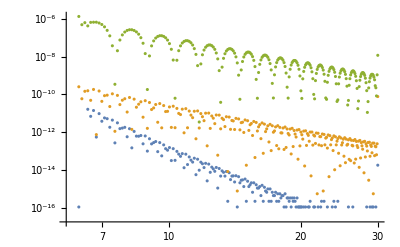

```mathematica
ListLogLogPlot[{FluxEnergy1PAchi2InfinityRelativeDifferenceOnGrid,FluxEnergy1PAchi2InfinityCubicSplineRelativeDifferenceOnGrid,FluxEnergy1PAchi2InfinityLoResCubicSplineRelativeDifferenceOnGrid}]
```

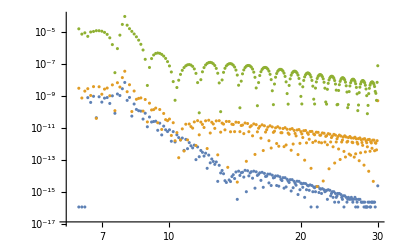

```mathematica
ListLogLogPlot[{FluxEnergy1PAchi2HorizonRelativeDifferenceOnGrid,FluxEnergy1PAchi2HorizonCubicSplineRelativeDifferenceOnGrid,FluxEnergy1PAchi2HorizonLoResCubicSplineRelativeDifferenceOnGrid}]
```

## 0PA amplitudes

### Data and interpolants

```mathematica
Amp0PADirectory
```

C:\Users\ap8e11\AppData\Roaming\Mathematica\Applications\WaSABI\InspiralModels\sf_amp_data\1SF\Schwarz_Circ

```mathematica
Do[Amp0PAGrid=Import[DownloadDirectory<>"Amplitudes1PAT1R.h5","0PA/Grid"];
Amp0PAData[l,m]=Import[DownloadDirectory<>"Amplitudes1PAT1R.h5","/0PA/l"<>ToString[l]<>"/m"<>ToString[m]<>"/Infinity"];
ReAmp0PAOnGrid[l,m]=Transpose[{Amp0PAGrid,Amp0PAData[l,m][[;;,1]]}];
ImAmp0PAOnGrid[l,m]=Transpose[{Amp0PAGrid,Amp0PAData[l,m][[;;,2]]}];
Amp0PA[l,m]=Function[r0,Evaluate[Interpolation[ReAmp0PAOnGrid[l,m],InterpolationOrder->8][r0]+I Interpolation[ImAmp0PAOnGrid[l,m],InterpolationOrder->8][r0]]];
Amp0PACubicSpline[l,m]=Function[r0,Evaluate[Interpolation[ReAmp0PAOnGrid[l,m],InterpolationOrder->3,Method->"Spline"][r0]+I Interpolation[ImAmp0PAOnGrid[l,m],InterpolationOrder->3,Method->"Spline"][r0]]];
ReAmp0PAOnGridLoRes[l,m]=ReAmp0PAOnGrid[l,m][[;;;;8]];
ImAmp0PAOnGridLoRes[l,m]=ImAmp0PAOnGrid[l,m][[;;;;8]];
Amp0PALoResCubicSpline[l,m]=Function[r0,Evaluate[Interpolation[ReAmp0PAOnGridLoRes[l,m],InterpolationOrder->3,Method->"Spline"][r0]+I Interpolation[ImAmp0PAOnGridLoRes[l,m],InterpolationOrder->3,Method->"Spline"][r0]]];
,{l,2,5},{m,0,l}]
```

```mathematica
Do[WaSABIteukAmp0PAOnGrid[l,m]=Import[Amp0PADirectory<>"/1SFTeukampSchwarzCirc"<>ToString[l]<>ToString[m]<>".m"];
WaSABIAmp0PAOnGrid[l,m]={#[[1]],(-2(-#[[2]]))/((ⅈ m √(1/(#[[1]])^3))^2)}& /@WaSABIteukAmp0PAOnGrid[l,m];
WaSABIteukAmp0PA[l,m]=Interpolation[WaSABIteukAmp0PAOnGrid[l,m],InterpolationOrder->8];
WaSABIAmp0PA[l,m][r0_]:=(-2(-WaSABIteukAmp0PA[l,m][r0]))/((ⅈ m √(1/r0^3))^2);
, {l,2,5},{m,1,l}]
```

```mathematica
rmin0PAAmp=Amp0PAGrid[[1]]
rmax0PAAmp=Amp0PAGrid[[-1]]
```

6.

29.9883

```mathematica
GraphicsGrid[Table[Plot[Amp0PACubicSpline[l,m][r0]//ReIm,{r0,rmin0PAAmp,rmax0PAAmp},PlotLegends->Placed["("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,0,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

### Comparison of interpolating functions

```mathematica
GraphicsGrid[Table[LogLogPlot[{Abs[1-Re[Amp0PACubicSpline[l,m][r0]]/Re[WaSABIAmp0PA[l,m][r0]]],Abs[1-Re[Amp0PALoResCubicSpline[l,m][r0]]/Re[WaSABIAmp0PA[l,m][r0]]]},{r0,rmin0PAAmp,rmax0PAAmp},PlotLegends->Placed["Re("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

```mathematica
GraphicsGrid[Table[LogLogPlot[{Abs[1-Im[Amp0PACubicSpline[l,m][r0]]/Im[WaSABIAmp0PA[l,m][r0]]],Abs[1-Im[Amp0PALoResCubicSpline[l,m][r0]]/Im[WaSABIAmp0PA[l,m][r0]]]},{r0,rmin0PAAmp,rmax0PAAmp},PlotLegends->Placed["Im("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

### Comparison of interpolant against raw WaSABI data

```mathematica
Do[ReAmp0PACubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Re[Amp0PACubicSpline[l,m][#[[1]]]]/Re[#[[2]]]]} & /@ WaSABIAmp0PAOnGrid[l,m]);
ImAmp0PACubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Im[Amp0PACubicSpline[l,m][#[[1]]]]/Im[#[[2]]]]} & /@ WaSABIAmp0PAOnGrid[l,m]);
ReAmp0PALoResCubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Re[Amp0PALoResCubicSpline[l,m][#[[1]]]]/Re[#[[2]]]]} & /@ WaSABIAmp0PAOnGrid[l,m]);
ImAmp0PALoResCubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Im[Amp0PALoResCubicSpline[l,m][#[[1]]]]/Im[#[[2]]]]} & /@ WaSABIAmp0PAOnGrid[l,m]);
,{l,2,5},{m,1,l}]
```

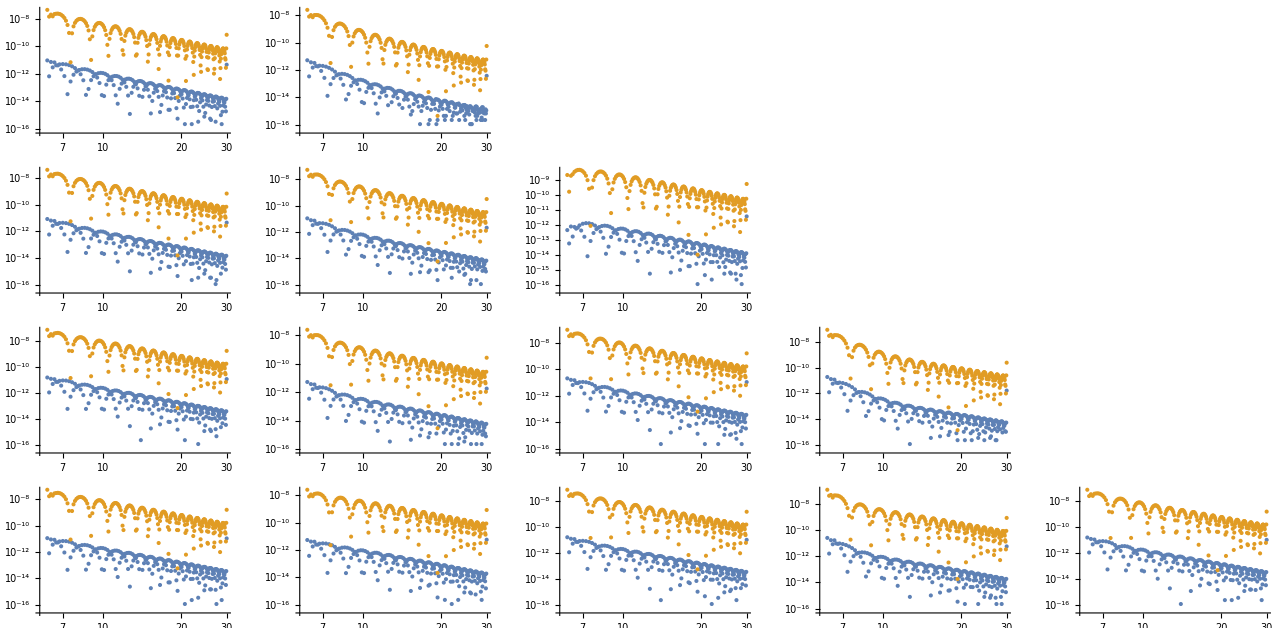

```mathematica
GraphicsGrid[Table[ListLogLogPlot[{ReAmp0PACubicSplineRelativeDifferenceOnGrid[l,m],ReAmp0PALoResCubicSplineRelativeDifferenceOnGrid[l,m]}],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

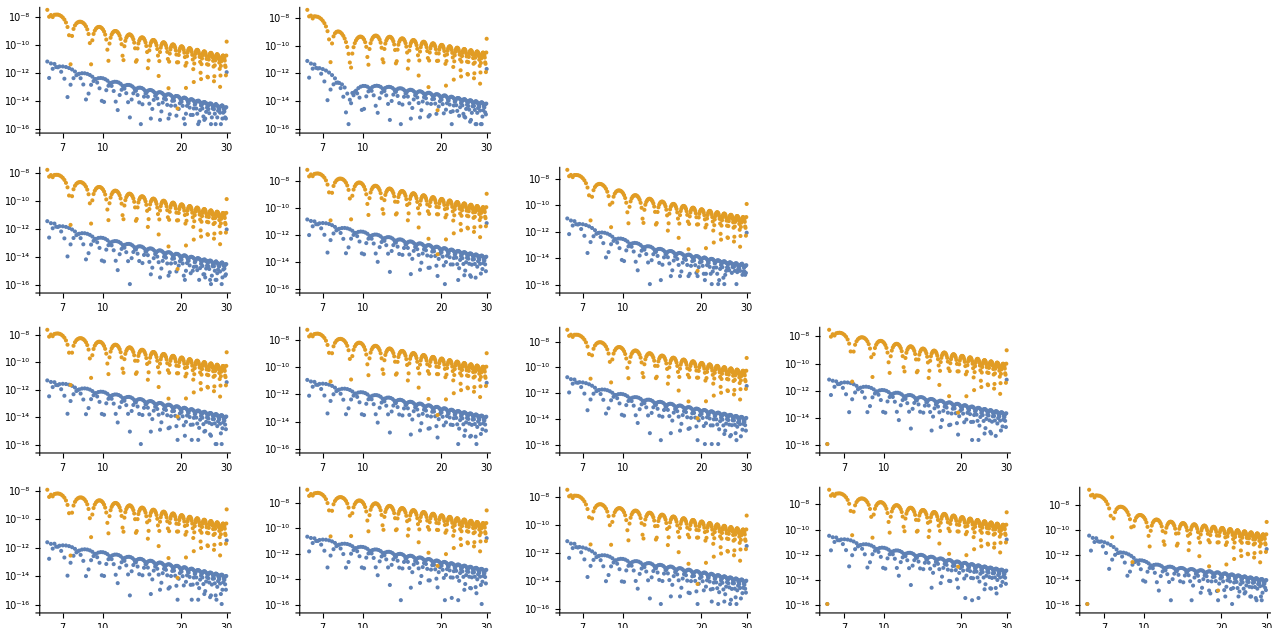

```mathematica
GraphicsGrid[Table[ListLogLogPlot[{ImAmp0PACubicSplineRelativeDifferenceOnGrid[l,m],ImAmp0PALoResCubicSplineRelativeDifferenceOnGrid[l,m]}],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

## 1PA amplitudes

### Data and interpolants

```mathematica
Do[Amp1PAGrid=Import[DownloadDirectory<>"Amplitudes1PAT1R.h5","1PA/Grid"];
Amp1PAData[l,m]=Import[DownloadDirectory<>"Amplitudes1PAT1R.h5","/1PA/l"<>ToString[l]<>"/m"<>ToString[m]<>"/Infinity"];
ReAmp1PAOnGrid[l,m]=Transpose[{Amp1PAGrid,Amp1PAData[l,m][[;;,1]]}];
ImAmp1PAOnGrid[l,m]=Transpose[{Amp1PAGrid,Amp1PAData[l,m][[;;,2]]}];
Amp1PA[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAOnGrid[l,m],InterpolationOrder->8][r0]+I Interpolation[ImAmp1PAOnGrid[l,m],InterpolationOrder->8][r0]]];
Amp1PACubicSpline[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAOnGrid[l,m],InterpolationOrder->3,Method->"Spline"][r0]+I Interpolation[ImAmp1PAOnGrid[l,m],InterpolationOrder->3,Method->"Spline"][r0]]];
ReAmp1PAOnGridLoRes[l,m]=ReAmp1PAOnGrid[l,m][[;;;;8]];
ImAmp1PAOnGridLoRes[l,m]=ImAmp1PAOnGrid[l,m][[;;;;8]];
Amp1PALoResCubicSpline[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAOnGridLoRes[l,m],InterpolationOrder->3,Method->"Spline"][r0]+I Interpolation[ImAmp1PAOnGridLoRes[l,m],InterpolationOrder->3,Method->"Spline"][r0]]];
,{l,2,5},{m,0,l}]
```

```mathematica
Do[WaSABIteukAmp1PAϵOnGrid[l,m]=Import[Amp1PADirectory<>"/2SFTeukampSchwarzCirc"<>ToString[l]<>ToString[m]<>".m"];
WaSABIAmp1PAϵOnGrid[l,m]={Exp[#[[1]]],(-2(Exp[#[[2]]]))/((ⅈ m √(1/(#[[1]])^3))^2)}& /@WaSABIteukAmp1PAϵOnGrid[l,m];
WaSABIteukAmp1PAϵ[l,m]=Function[r0,Exp[Interpolation[WaSABIteukAmp1PAϵOnGrid[l,m],InterpolationOrder->3][Log[r0]]]];
WaSABIAmp1PAϵ[l,m][r0_]:=(-2(WaSABIteukAmp1PAϵ[l,m][r0]))/((ⅈ m √(1/r0^3))^2);
WaSABIAmp1PA[l,m][r0_]:=WaSABIAmp0PA[l,m][r0]+WaSABIAmp1PAϵ[l,m][r0]+2/3 r0 (1+(-(1/r0)/Sqrt[1-3/r0])) WaSABIAmp0PA[l,m]'[r0];
, {l,2,5},{m,1,l}]
```

```mathematica
rmin1PAAmp=Amp1PAGrid[[1]]
rmax1PAAmp=Amp1PAGrid[[-1]]
```

6.25

29.9884

```mathematica
GraphicsGrid[Table[Plot[Amp1PACubicSpline[l,m][r0]//ReIm,{r0,rmin1PAAmp,rmax1PAAmp},PlotLegends->Placed["("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,0,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

```mathematica
GraphicsGrid[Table[Plot[WaSABIAmp1PA[l,m][r0]//ReIm,{r0,rmin1PAAmp,rmax1PAAmp},PlotLegends->Placed["("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,0,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

### Comparison of interpolating functions

```mathematica
GraphicsGrid[Table[LogLogPlot[{Abs[1-Re[Amp1PACubicSpline[l,m][r0]]/Re[WaSABIAmp1PA[l,m][r0]]],Abs[1-Re[Amp1PALoResCubicSpline[l,m][r0]]/Re[WaSABIAmp1PA[l,m][r0]]]},{r0,rmin1PAAmp,rmax1PAAmp},PlotLegends->Placed["Re("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

```mathematica
GraphicsGrid[Table[LogLogPlot[{Abs[1-Im[Amp1PACubicSpline[l,m][r0]]/Im[WaSABIAmp1PA[l,m][r0]]],Abs[1-Im[Amp1PALoResCubicSpline[l,m][r0]]/Im[WaSABIAmp1PA[l,m][r0]]]},{r0,rmin1PAAmp,rmax1PAAmp},PlotLegends->Placed["Im("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

### Comparison of interpolant against raw WaSABI data

```mathematica
Do[ReAmp1PACubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Re[Amp1PACubicSpline[l,m][#[[1]]]]/Re[#[[2]]]]} & /@ WaSABIAmp1PAOnGrid[l,m]);
ImAmp1PACubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Im[Amp1PACubicSpline[l,m][#[[1]]]]/Im[#[[2]]]]} & /@ WaSABIAmp1PAOnGrid[l,m]);
ReAmp1PALoResCubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Re[Amp1PALoResCubicSpline[l,m][#[[1]]]]/Re[#[[2]]]]} & /@ WaSABIAmp1PAOnGrid[l,m]);
ImAmp1PALoResCubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Im[Amp1PALoResCubicSpline[l,m][#[[1]]]]/Im[#[[2]]]]} & /@ WaSABIAmp1PAOnGrid[l,m]);
,{l,2,5},{m,1,l}]
```

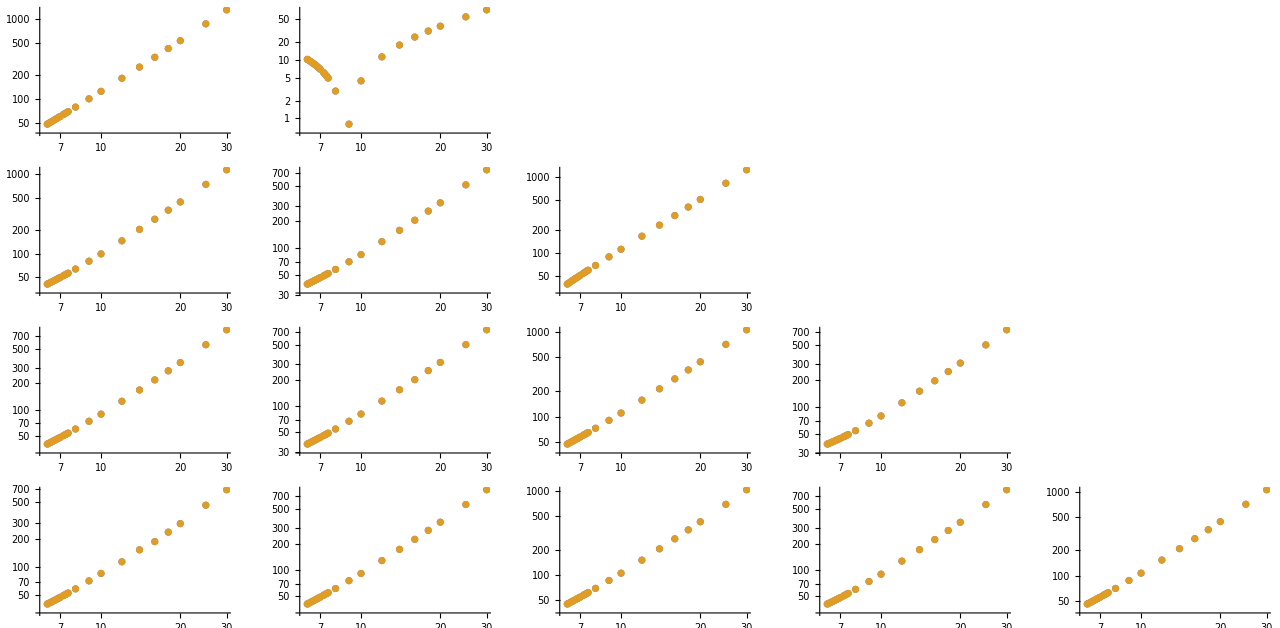

```mathematica
GraphicsGrid[Table[ListLogLogPlot[{ReAmp1PACubicSplineRelativeDifferenceOnGrid[l,m],ReAmp1PALoResCubicSplineRelativeDifferenceOnGrid[l,m]}],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

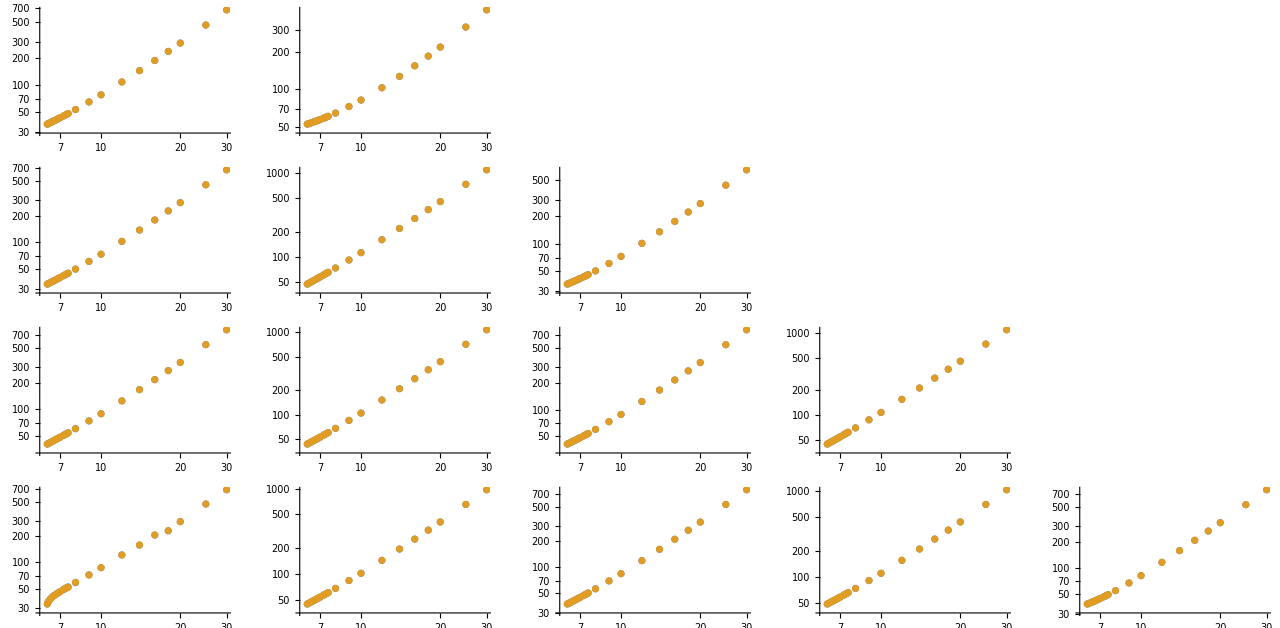

```mathematica
GraphicsGrid[Table[ListLogLogPlot[{ImAmp1PACubicSplineRelativeDifferenceOnGrid[l,m],ImAmp1PALoResCubicSplineRelativeDifferenceOnGrid[l,m]}],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

## 1PA χ_1 amplitudes

### Data and interpolants

```mathematica
Do[Amp1PAchi1Grid=Import[DownloadDirectory<>"Amplitudes1PAT1R.h5","1PAchi1/Grid"];
Amp1PAchi1Data[l,m]=Import[DownloadDirectory<>"Amplitudes1PAT1R.h5","/1PAchi1/l"<>ToString[l]<>"/m"<>ToString[m]<>"/Infinity"];
ReAmp1PAchi1OnGrid[l,m]=Transpose[{Amp1PAchi1Grid,Amp1PAchi1Data[l,m][[;;,1]]}];
ImAmp1PAchi1OnGrid[l,m]=Transpose[{Amp1PAchi1Grid,Amp1PAchi1Data[l,m][[;;,2]]}];
Amp1PAchi1[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAchi1OnGrid[l,m],InterpolationOrder->8][r0]+I Interpolation[ImAmp1PAchi1OnGrid[l,m],InterpolationOrder->8][r0]]];
Amp1PAchi1CubicSpline[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAchi1OnGrid[l,m],InterpolationOrder->3,Method->"Spline"][r0]+I Interpolation[ImAmp1PAchi1OnGrid[l,m],InterpolationOrder->3,Method->"Spline"][r0]]];
ReAmp1PAchi1OnGridLoRes[l,m]=ReAmp1PAchi1OnGrid[l,m][[;;;;8]];
ImAmp1PAchi1OnGridLoRes[l,m]=ImAmp1PAchi1OnGrid[l,m][[;;;;8]];
Amp1PAchi1LoResCubicSpline[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAchi1OnGridLoRes[l,m],InterpolationOrder->3,Method->"Spline"][r0]+I Interpolation[ImAmp1PAchi1OnGridLoRes[l,m],InterpolationOrder->3,Method->"Spline"][r0]]];
,{l,2,5},{m,0,l}]
```

```mathematica
Do[WaSABIteukAmp1PAchi1OnGrid[l,m]=Import[Amp1PAchi1Directory<>"/Slow_chi1_TeukampSchwarzCirc"<>ToString[l]<>ToString[m]<>".m"];
WaSABIAmp1PAchi1OnGrid[l,m]={#[[1]],(-2(-#[[2]]))/((ⅈ m √(1/(#[[1]])^3))^2)}& /@WaSABIteukAmp1PAchi1OnGrid[l,m];
WaSABIteukAmp1PAchi1[l,m]=Interpolation[WaSABIteukAmp1PAchi1OnGrid[l,m],InterpolationOrder->8];
WaSABIAmp1PAchi1[l,m][r0_]:=(-2(-WaSABIteukAmp1PAchi1[l,m][r0]))/((ⅈ m √(1/r0^3))^2);
, {l,2,5},{m,1,l}]
```

```mathematica
rmin1PAchi1Amp=Amp1PAchi1Grid[[1]]
rmax1PAchi1Amp=Amp1PAchi1Grid[[-1]]
```

6.1

29.9883

```mathematica
GraphicsGrid[Table[Plot[Amp1PAchi1CubicSpline[l,m][r0]//ReIm,{r0,rmin1PAchi1Amp,rmax1PAchi1Amp},PlotLegends->Placed["("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,0,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

### Comparison of interpolating functions

```mathematica
GraphicsGrid[Table[LogLogPlot[{Abs[1-Re[Amp1PAchi1CubicSpline[l,m][r0]]/Re[WaSABIAmp1PAchi1[l,m][r0]]],Abs[1-Re[Amp1PAchi1LoResCubicSpline[l,m][r0]]/Re[WaSABIAmp1PAchi1[l,m][r0]]]},{r0,rmin1PAchi1Amp,rmax1PAchi1Amp},PlotLegends->Placed["Re("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

```mathematica
GraphicsGrid[Table[LogLogPlot[{Abs[1-Im[Amp1PAchi1CubicSpline[l,m][r0]]/Im[WaSABIAmp1PAchi1[l,m][r0]]],Abs[1-Im[Amp1PAchi1LoResCubicSpline[l,m][r0]]/Im[WaSABIAmp1PAchi1[l,m][r0]]]},{r0,rmin1PAchi1Amp,rmax1PAchi1Amp},PlotLegends->Placed["Im("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

### Comparison of interpolant against raw WaSABI data

```mathematica
Do[ReAmp1PAchi1CubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Re[Amp1PAchi1CubicSpline[l,m][#[[1]]]]/Re[#[[2]]]]} & /@ WaSABIAmp1PAchi1OnGrid[l,m]);
ImAmp1PAchi1CubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Im[Amp1PAchi1CubicSpline[l,m][#[[1]]]]/Im[#[[2]]]]} & /@ WaSABIAmp1PAchi1OnGrid[l,m]);
ReAmp1PAchi1LoResCubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Re[Amp1PAchi1LoResCubicSpline[l,m][#[[1]]]]/Re[#[[2]]]]} & /@ WaSABIAmp1PAchi1OnGrid[l,m]);
ImAmp1PAchi1LoResCubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Im[Amp1PAchi1LoResCubicSpline[l,m][#[[1]]]]/Im[#[[2]]]]} & /@ WaSABIAmp1PAchi1OnGrid[l,m]);
,{l,2,5},{m,1,l}]
```

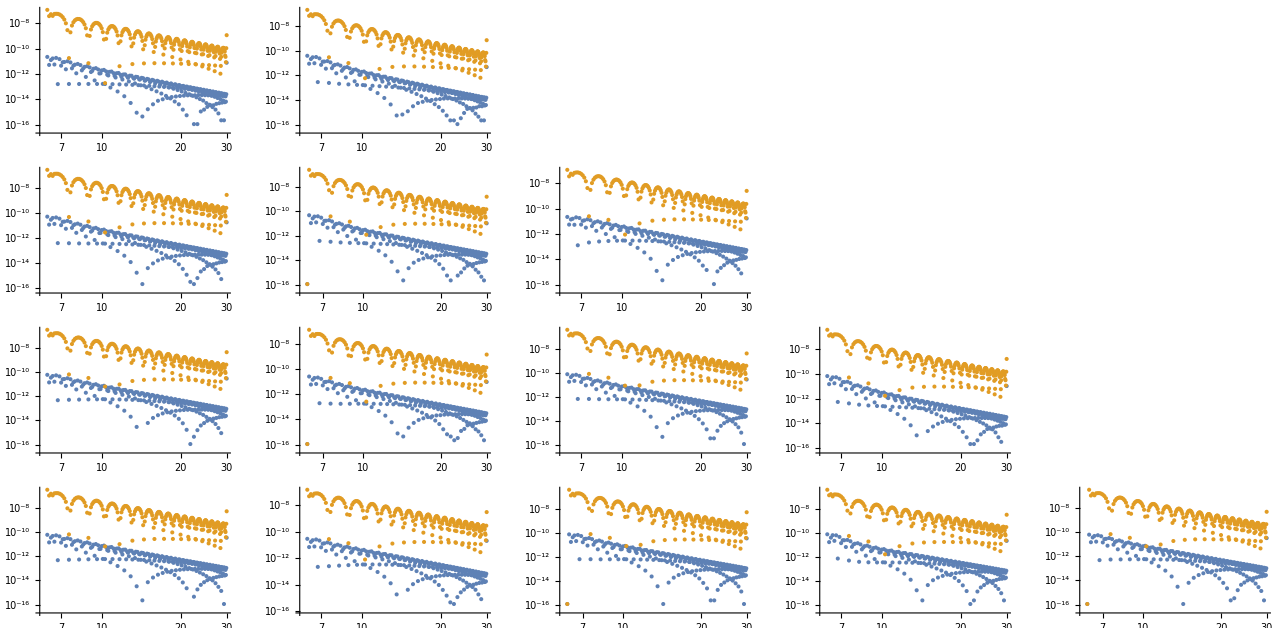

```mathematica
GraphicsGrid[Table[ListLogLogPlot[{ReAmp1PAchi1CubicSplineRelativeDifferenceOnGrid[l,m],ReAmp1PAchi1LoResCubicSplineRelativeDifferenceOnGrid[l,m]}],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

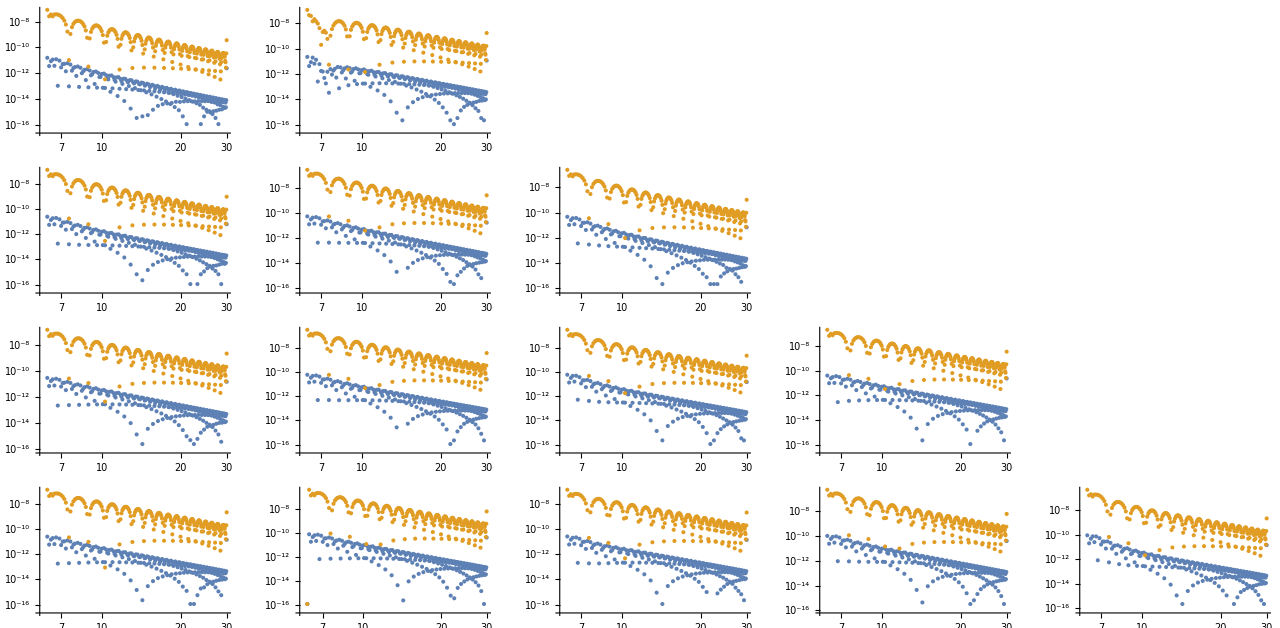

```mathematica
GraphicsGrid[Table[ListLogLogPlot[{ImAmp1PAchi1CubicSplineRelativeDifferenceOnGrid[l,m],ImAmp1PAchi1LoResCubicSplineRelativeDifferenceOnGrid[l,m]}],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

## 1PA χ_2 amplitudes

### Data and interpolants

```mathematica
Do[Amp1PAchi2Grid=Import[DownloadDirectory<>"Amplitudes1PAT1R.h5","1PAchi2/Grid"];
Amp1PAchi2Data[l,m]=Import[DownloadDirectory<>"Amplitudes1PAT1R.h5","/1PAchi2/l"<>ToString[l]<>"/m"<>ToString[m]<>"/Infinity"];
ReAmp1PAchi2OnGrid[l,m]=Transpose[{Amp1PAchi2Grid,Amp1PAchi2Data[l,m][[;;,1]]}];
ImAmp1PAchi2OnGrid[l,m]=Transpose[{Amp1PAchi2Grid,Amp1PAchi2Data[l,m][[;;,2]]}];
Amp1PAchi2[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAchi2OnGrid[l,m],InterpolationOrder->8][r0]+I Interpolation[ImAmp1PAchi2OnGrid[l,m],InterpolationOrder->8][r0]]];
Amp1PAchi2CubicSpline[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAchi2OnGrid[l,m],InterpolationOrder->3,Method->"Spline"][r0]+I Interpolation[ImAmp1PAchi2OnGrid[l,m],InterpolationOrder->3,Method->"Spline"][r0]]];
ReAmp1PAchi2OnGridLoRes[l,m]=ReAmp1PAchi2OnGrid[l,m][[;;;;8]];
ImAmp1PAchi2OnGridLoRes[l,m]=ImAmp1PAchi2OnGrid[l,m][[;;;;8]];
Amp1PAchi2LoResCubicSpline[l,m]=Function[r0,Evaluate[Interpolation[ReAmp1PAchi2OnGridLoRes[l,m],InterpolationOrder->3,Method->"Spline"][r0]+I Interpolation[ImAmp1PAchi2OnGridLoRes[l,m],InterpolationOrder->3,Method->"Spline"][r0]]];
,{l,2,5},{m,0,l}]
```

```mathematica
Do[RWZfactor[l]=Sqrt[(l-1)l(l+1)(l+2)]/2;
WaSABIRWZAmp1PAchi2OnGrid[l,m]=Import[Amp1PAchi2Directory<>"/chi2_2SF_RWZampSchwarzCirc"<>ToString[l]<>ToString[m]<>".m"];
WaSABIAmp1PAchi2OnGrid[l,m]={#[[1]],RWZfactor[l]If[EvenQ[l+m],#[[2]], -I #[[2]]]}& /@WaSABIRWZAmp1PAchi2OnGrid[l,m];
WaSABIRWZAmp1PAchi2[l,m]=Interpolation[WaSABIRWZAmp1PAchi2OnGrid[l,m],InterpolationOrder->8];
WaSABIAmp1PAchi2[l,m][r0_]:=RWZfactor[l] If[EvenQ[l+m],WaSABIRWZAmp1PAchi2[l,m][r0], -I WaSABIRWZAmp1PAchi2[l,m][r0]];
, {l,2,5},{m,1,l}]
```

```mathematica
rmin1PAchi2Amp=Amp1PAchi2Grid[[1]]
rmax1PAchi2Amp=Amp1PAchi2Grid[[-1]]
```

6.1

29.9883

```mathematica
GraphicsGrid[Table[Plot[Amp1PAchi2CubicSpline[l,m][r0]//ReIm,{r0,rmin1PAchi2Amp,rmax1PAchi2Amp},PlotLegends->Placed["("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,0,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

### Comparison of interpolating functions

```mathematica
GraphicsGrid[Table[LogLogPlot[{Abs[1-Re[Amp1PAchi2CubicSpline[l,m][r0]]/Re[WaSABIAmp1PAchi2[l,m][r0]]],Abs[1-Re[Amp1PAchi2LoResCubicSpline[l,m][r0]]/Re[WaSABIAmp1PAchi2[l,m][r0]]]},{r0,rmin1PAchi2Amp,rmax1PAchi2Amp},PlotLegends->Placed["Re("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

```mathematica
GraphicsGrid[Table[LogLogPlot[{Abs[1-Im[Amp1PAchi2CubicSpline[l,m][r0]]/Im[WaSABIAmp1PAchi2[l,m][r0]]],Abs[1-Im[Amp1PAchi2LoResCubicSpline[l,m][r0]]/Im[WaSABIAmp1PAchi2[l,m][r0]]]},{r0,rmin1PAchi2Amp,rmax1PAchi2Amp},PlotLegends->Placed["Im("<>ToString[l]<>","<>ToString[m]<>")",Above]],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

-Graphics-

### Comparison of interpolant against raw WaSABI data

```mathematica
Do[ReAmp1PAchi2CubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Re[Amp1PAchi2CubicSpline[l,m][#[[1]]]]/Re[#[[2]]]]} & /@ WaSABIAmp1PAchi2OnGrid[l,m]);
ImAmp1PAchi2CubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Im[Amp1PAchi2CubicSpline[l,m][#[[1]]]]/Im[#[[2]]]]} & /@ WaSABIAmp1PAchi2OnGrid[l,m]);
ReAmp1PAchi2LoResCubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Re[Amp1PAchi2LoResCubicSpline[l,m][#[[1]]]]/Re[#[[2]]]]} & /@ WaSABIAmp1PAchi2OnGrid[l,m]);
ImAmp1PAchi2LoResCubicSplineRelativeDifferenceOnGrid[l,m]=({#[[1]], Abs[1 - Im[Amp1PAchi2LoResCubicSpline[l,m][#[[1]]]]/Im[#[[2]]]]} & /@ WaSABIAmp1PAchi2OnGrid[l,m]);
,{l,2,5},{m,1,l}]
```

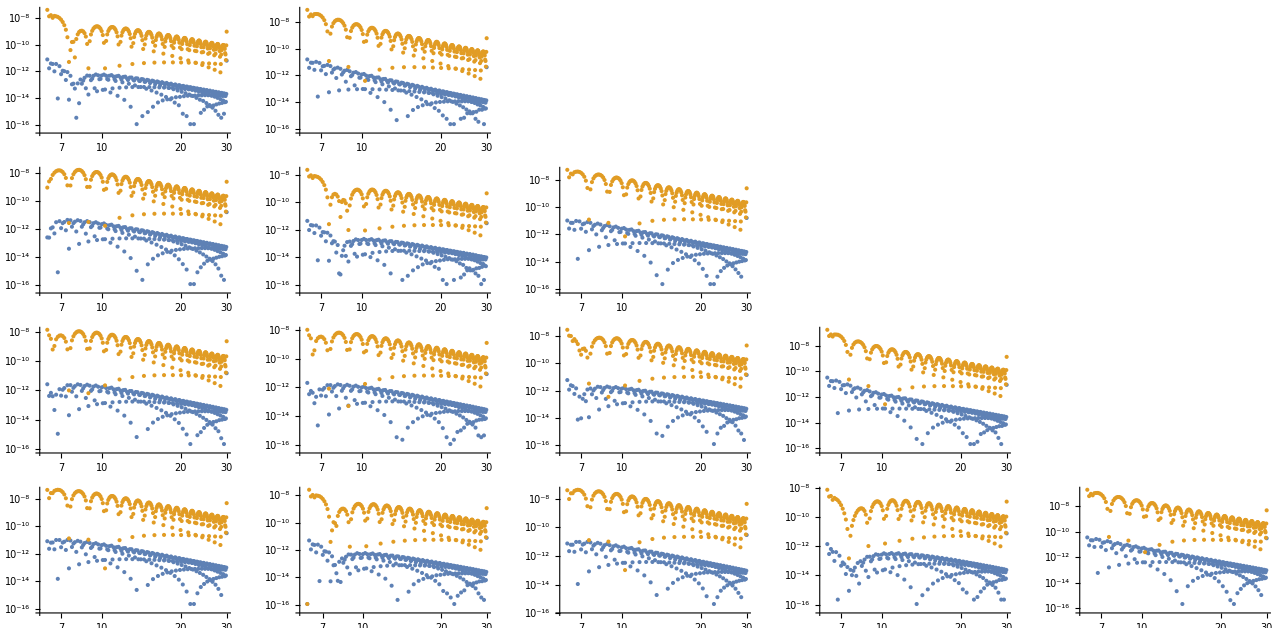

```mathematica
GraphicsGrid[Table[ListLogLogPlot[{ReAmp1PAchi2CubicSplineRelativeDifferenceOnGrid[l,m],ReAmp1PAchi2LoResCubicSplineRelativeDifferenceOnGrid[l,m]}],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```

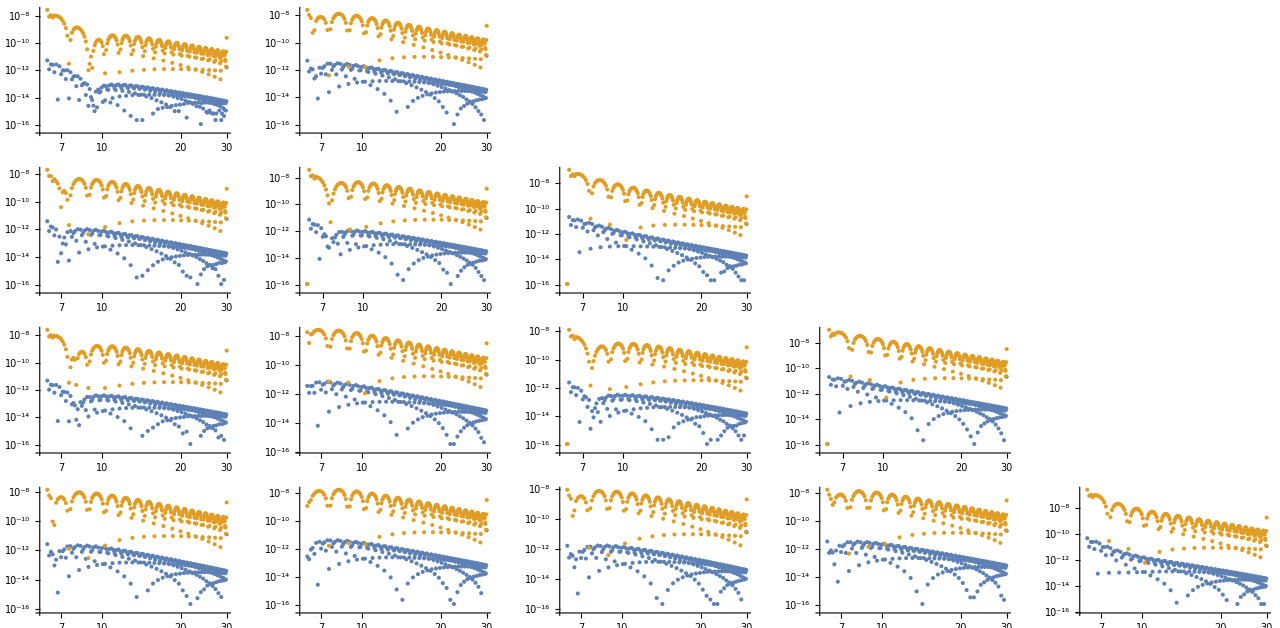

```mathematica
GraphicsGrid[Table[ListLogLogPlot[{ImAmp1PAchi2CubicSplineRelativeDifferenceOnGrid[l,m],ImAmp1PAchi2LoResCubicSplineRelativeDifferenceOnGrid[l,m]}],{l,2,5},{m,1,l}],ImageSize->1280,Alignment->{Right,Top}]
```